```mathematica
ClearAll["Global`*"];

(*1. Echten Datensatz aus dem Internet laden*)
url="https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data";

rawData=Import[url,"CSV"];

(*Leere Abschlusszeile entfernen*)
rawData=Select[rawData,Length[#]==5&];

(*Spalten:1 Kelchblattlänge 2 Kelchblattbreite 3 Blütenblattlänge 4 Blütenblattbreite 5 tatsächliche Pflanzenart*)

measurements=N[rawData[[All,1;;4]]];
species=rawData[[All,5]];

Length[measurements]
```

150

```mathematica
{}
```

{}

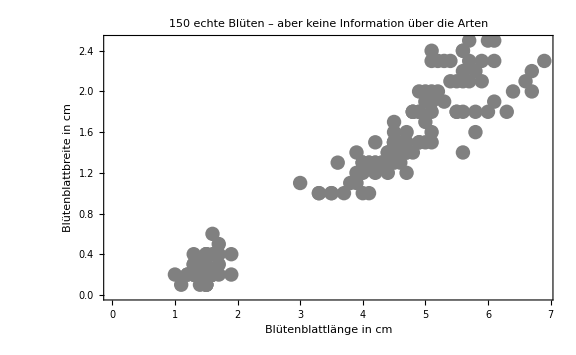

```mathematica
plotPoints=measurements[[All,{3,4}]];

unlabeledPlot=ListPlot[plotPoints,PlotStyle->Directive[Gray,PointSize[0.018]],Frame->True,FrameLabel->{"Blütenblattlänge in cm","Blütenblattbreite in cm"},PlotLabel->"150 echte Blüten – aber keine Information über die Arten",ImageSize->Large];

unlabeledPlot
```

```mathematica
standardizedData=Standardize[measurements];

clusterIDs=ClusteringComponents[standardizedData,3,1,Method->"KMeans"];

clusterIDs
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,1,1,1,2,1,2,1,2,1,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,1,1,1,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1}

{150}

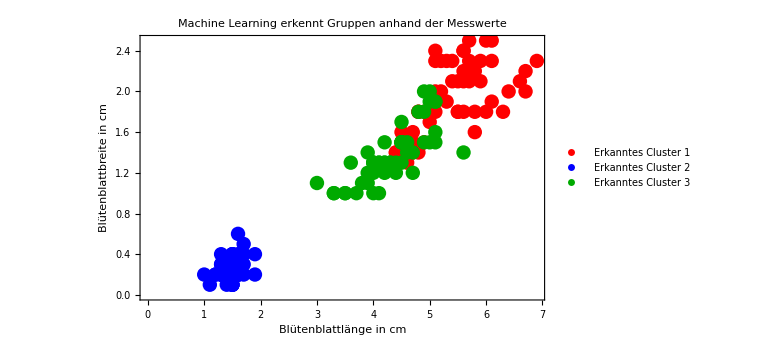

```mathematica
(*Jede Spalte separat standardisieren*)
standardizedData=Standardize[measurements];

(*Jede Zeile ausdrücklich als einen vierdimensionalen Datenpunkt behandeln*)
clusterIDs=ClusteringComponents[standardizedData,3,1,DistanceFunction->EuclideanDistance,Method->"KMeans"];

Dimensions[clusterIDs]
clusterGroups=Table[Pick[plotPoints,clusterIDs,clusterNumber],{clusterNumber,3}];

clusterPlot=ListPlot[clusterGroups,PlotStyle->{Directive[Red,PointSize[0.018]],Directive[Blue,PointSize[0.018]],Directive[Darker[Green],PointSize[0.018]]},PlotLegends->{"Erkanntes Cluster 1","Erkanntes Cluster 2","Erkanntes Cluster 3"},Frame->True,FrameLabel->{"Blütenblattlänge in cm","Blütenblattbreite in cm"},PlotLabel->"Machine Learning erkennt Gruppen anhand der Messwerte",ImageSize->Large];

clusterPlot
```

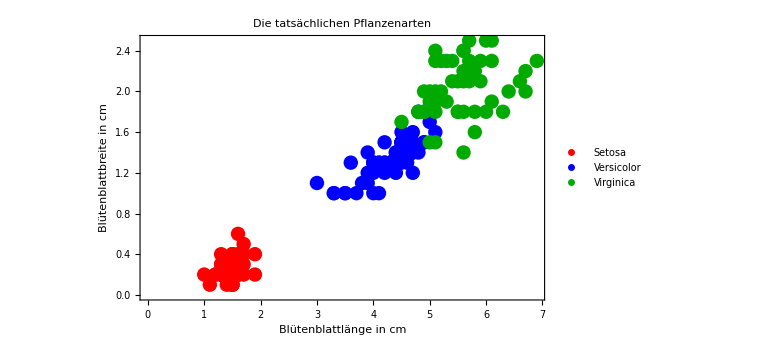

```mathematica
speciesNames={"Iris-setosa","Iris-versicolor","Iris-virginica"};

realGroups=Table[Pick[plotPoints,species,speciesName],{speciesName,speciesNames}];

realityPlot=ListPlot[realGroups,PlotStyle->{Directive[Red,PointSize[0.018]],Directive[Blue,PointSize[0.018]],Directive[Darker[Green],PointSize[0.018]]},PlotLegends->{"Setosa","Versicolor","Virginica"},Frame->True,FrameLabel->{"Blütenblattlänge in cm","Blütenblattbreite in cm"},PlotLabel->"Die tatsächlichen Pflanzenarten",ImageSize->Large];

realityPlot
```